```mathematica
Needs["EDA`"]
```

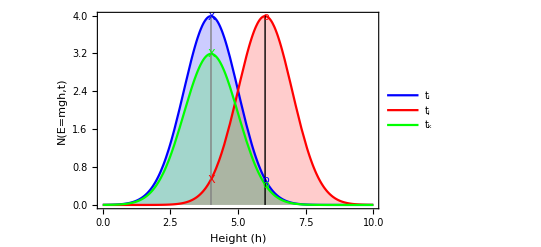

```mathematica
lineStyle={Thick,Gray};
lineStyle0={Thick,Black};
lineStyle3={Thick,Black};
lineStyle2={Thin,Blue};
lineStyle1={Thin,Red};
lineStyle4={Thick,Green};
line1=Line[{{4,0},{4,4}}];
line2=Line[{{6,0},{6,4}}];
Plot[{10PDF[NormalDistribution[4,1],xx],10PDF[NormalDistribution[6,1],xx],8PDF[NormalDistribution[4,1],xx]},{xx,0,10},Frame->True,Filling->Axis,PlotStyle->{Blue,Red,Green},FrameLabel->{"Height (h)","N(E=mgh,t)"},TicksStyle->Directive[FontSize->40],LabelStyle->{Black,18},ImageSize->{1000},PlotLegends->{"t_i","t_j","t_k"},Epilog->{
{Directive[lineStyle],line1,Text[Style["h_S",FontSize->Large],{4,4.1}]},
{Directive[lineStyle0],line2,Text[Style["h_W2",FontSize->Large],{6,4.1}]},
{Directive[lineStyle2],Text[Style["X",FontSize->Large],{4.01,3.97}],Text[Style["o",FontSize->Large],{6.01,.52}]},
{Directive[lineStyle4],Text[Style["X",FontSize->Large],{4.01,3.18}],Text[Style["o",FontSize->Large],{6.01,.43}]},
{Directive[lineStyle1],Text[Style["o",FontSize->Large],{6.01,3.98}],Text[Style["X",FontSize->Large],{4.01,.52}]}
}]
```

```mathematica
ratio1=N[10PDF[NormalDistribution[6,1],4]]/N[10PDF[NormalDistribution[6,1],6]]
ratio2=N[10PDF[NormalDistribution[4,1],4]]/N[10PDF[NormalDistribution[4,1],6]]
ratio3=N[8PDF[NormalDistribution[4,1],4]]/N[8PDF[NormalDistribution[4,1],6]]
```

0.135335

7.38906

7.38906

```mathematica
N[10PDF[NormalDistribution[4,1],4]]
N[10PDF[NormalDistribution[4,1],6]]

N[10PDF[NormalDistribution[6,1],4]]
N[10PDF[NormalDistribution[6,1],6]]

N[8PDF[NormalDistribution[4,1],4]]
N[8PDF[NormalDistribution[4,1],6]]
```

3.98942

0.53991

0.53991

3.98942

3.19154

0.431928